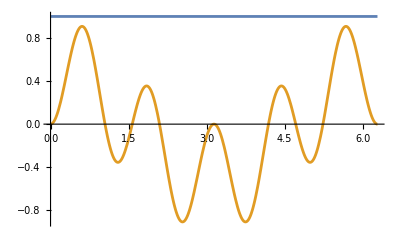

```mathematica
h[n_,t_]:= Sin[n t]
g[m_,t_]:=Cos[m t]
Plot[ {1,h[2,t]h[3,t]},{t, 0, 2π}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.1269×10^-7}. NIntegrate obtained -6.93889×10^-17 and 7.54866×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.282838474497808334794102247400360283791087567806243896484375}. NIntegrate obtained 6.93889×10^-17 and 9.3929×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.2831852015207019072675995597764692091047322719532530754804611206}. NIntegrate obtained -2.17708×10^-15 and 4.23158×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.396593-2.20872×10^-17 Cos[t]+0.105616 Cos[2 t]-6.92985×10^-16 Cos[3 t]-0.0773603 Cos[4 t]-1.13197×10^-16 Cos[5 t]+0.0719434 Cos[6 t]-0.279289 Sin[t]+2.20872×10^-17 Sin[2 t]+0.0704108 Sin[3 t]-1.91882×10^-17 Sin[4 t]+0.27197 Sin[5 t]-8.0066×10^-17 Sin[6 t]

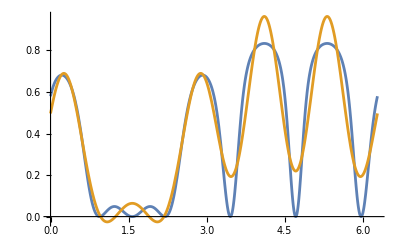

```mathematica
f[t_]:=Log[ArcTan[( Cos[3 t]+ Sin[2t])^2]+1]
a[0]:=NIntegrate[f[t],{t, 0, 2π}]/(2π)
a[n_]:=NIntegrate[f[t] Cos[n t],{t, 0, 2π}]/π
b[n_]:=NIntegrate[f[t] Sin[n t],{t, 0, 2π}]/π
FS[t_]= a[0]+Sum[ a[i]Cos[i t]+b[i] Sin[i t],{i,1,6}]
Plot[{f[t],FS[t]},{t, 0, 2 π}]
```

```mathematica
Table[
Integrate[g[i,t]g[i,t],{t,0, 2π}],
{i, 0, 10}]
```

{2 π,π,π,π,π,π,π,π,π,π,π}